```mathematica
teoricos = Import["teorico.csv", "Dataset", "HeaderLines"->1];
```

```mathematica
sim = Import["C:\\Users\\pdbru\\Desktop\\tesis\\haar-avg-sim.csv", "Dataset", "HeaderLines"->1];
```

```mathematica
busqueda[pA_, pB_] := Function[row, row["pA"] ==pA && row["pB"] ==pB ];
```

```mathematica
GraficarDiferencias[chA_, chB_, d_] := With[{
filtro = Select[(#chA == chA && #chB == chB && #d ==d)&]
}, 
ListDensityPlot[teoricos[filtro,{"pA","pB", "score"}][All, {#pA, #pB, #score  - sim[filtro,{"pA","pB", "score"}][SortBy[{#pA &, #pB &}]][SelectFirst[busqueda[#pA, #pB]], "score"]}&], PlotLegends->Automatic, InterpolationOrder->3, PlotTheme->"Scientific"]]
```

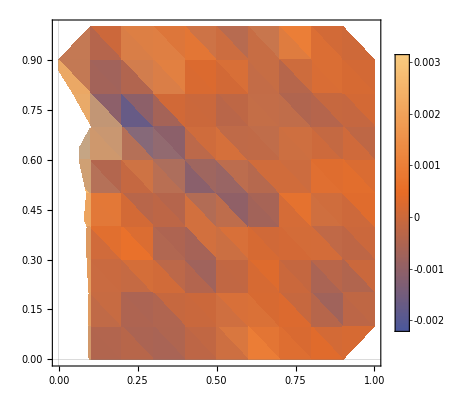

```mathematica
GraficarDiferencias["DC", "ADC", "fidelity"]
```

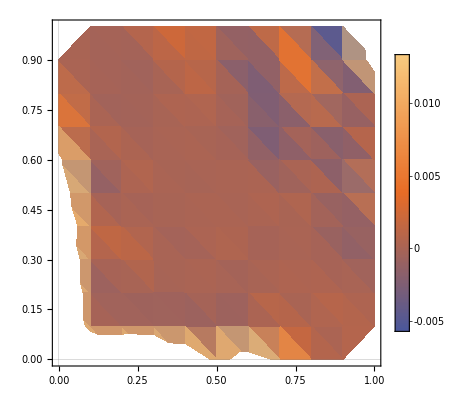

```mathematica
GraficarDiferencias["ADC", "ADC", "fidelity"]
```

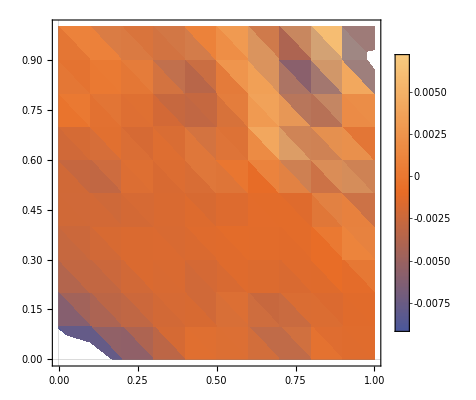

```mathematica
GraficarDiferencias["ADC", "ADC", "trace_distance"]
```